```mathematica
SetDirectory["/home/ethan/spring2020/computational/comphys/week1/assignment1/report/"]
```

/home/ethan/spring2020/computational/comphys/week1/assignment1/report

```mathematica
data=ReadList["/home/ethan/spring2020/computational/comphys/week1/assignment1/code/cor_1_1_0_3.14_2_1.txt",
{Number,Number}];
Export["plot11.pdf",ListPlot[data,
Frame->True,
FrameLabel->{"X (Arbitrary Units)", "Y (Arbitrary Units)" },
PlotLabel->"Lissajous Figure: Δϕ=π, ω_x/ω_y √5"]]
```

plot11.pdf

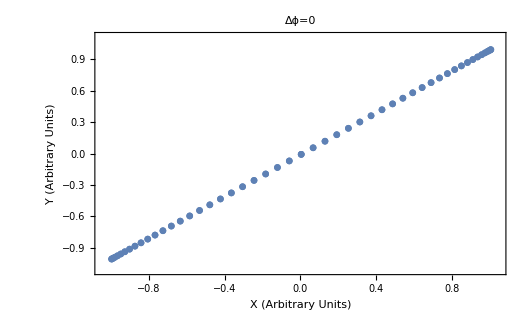

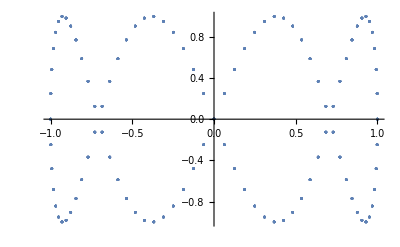

-Graphics-

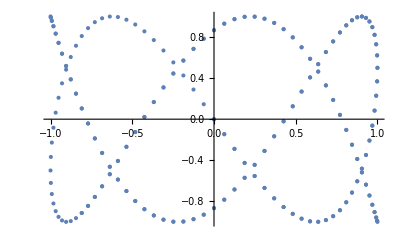

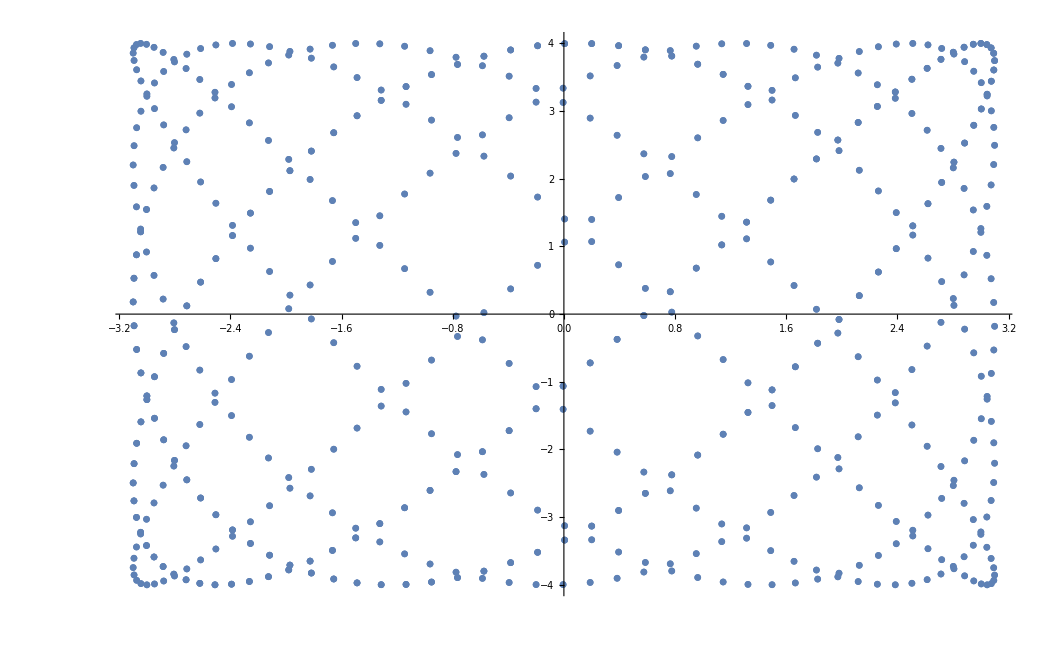

```mathematica
ListPlot[data]
```

```mathematica
N[Pi,20]
```

3.1415926535897932385

```mathematica
exact= N[Integrate[Exp[x],
{x,0,1}],20]
```

1.7182818284590452354

```mathematica
Print[exact]
```

1.7182818284590452354

```mathematica
{{0.15707963267948966,{2.6321485776217566}},{0.015707963267948967,{2.9021504328396035}},{0.0015707963267948967,{2.9298708222681946}},{0.00015707963267948965,{2.932650066536867}}}
```

```mathematica
SetDirectory["/home/ethan/spring2020/computational/comphys/week2"]
```

/home/ethan/spring2020/computational/comphys/week2

```mathematica
getres[n_]:=ReadList["!./integrate " <>ToString[n]<>" | awk '{print $2}'", Number][[1]]
```

```mathematica
res = 
Table[
{1/n,Abs[(getres[n]-exact)/exact]},{n, {10, 100, 1000, 10000, 100000, 1000000, 10000000, 100000000, 1000000000, 10000000000, 100000000000}}]
```

{{1/10,0.00102734},{1/100,0.0000102808},{1/1000,1.02808×10^-7},{1/10000,1.02809×10^-9},{1/100000,1.02748×10^-11},{1/1000000,9.14872×10^-14},{1/10000000,1.94629×10^-14},{1/100000000,5.6524×10^-14},{1/1000000000,8.71751×10^-14},{1/10000000000,6.20015×10^-14},{1/100000000000,1.3018×10^-13}}

```mathematica
Export["test.pdf", ListLogLogPlot[
res,
 Frame->True,
 PlotRange->All]]
```

test.pdf

```mathematica
{{0.15707963267948966,2.6321485776217566},{0.015707963267948967,2.9021504328396035},{0.0015707963267948967,2.9298708222681946},{0.00015707963267948965,2.932650066536867}}
```

{{0.15708,2.63215},{0.015708,2.90215},{0.0015708,2.92987},{0.00015708,2.93265}}